```mathematica
(* A Monte Carlo simulation of gas breakdown between parallel plates *)
(* nc is the distance between plates, expressed as the number of collision lengths *)(* ni is the voltage, expressed as a multiple of the ionization voltage *)
(* reps is the number of electrons to toss *)
PaschenMcPlatesWeighted[nc_,ni_,reps_]:=Module[{results},
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons,weight},
nIons=0;
x0=0;
weight=1;
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion. *)
If[ni/nc(x1-x0)>1,nIons+=weight;weight*=2];
x0=x1;
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

## Banked Parallel Plate MC

```mathematica
(* A Monte Carlo simulation of gas breakdown between parallel plates *)
(* nc is the distance between plates, expressed as the number of collision lengths *)(* ni is the voltage, expressed as a multiple of the ionization voltage *)
(* reps is the number of electrons to toss *)
PaschenMcPlatesBanked[nc_,ni_,reps_]:=Module[{results,stack},
stack = CreateDataStructure["Stack"];
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons},
nIons=0;
stack["Push",0];
While[!stack["EmptyQ"],
x0=stack["Pop"];
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion, push the newly freed electron
onto the stack, and Sow the position where the ion was created. *)
If[ni/nc(x1-x0)>1,nIons++;stack["Push",x1];Sow[x1]];
x0=x1;
];
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

```mathematica
PaschenMcPlatesBanked[10,10,1000]
```

11.670.18

```mathematica
TableForm[tb=Table[Timing[{n,PaschenMcPlatesBanked[n,n,100]}],{n,1,32}]]
```

0. | 1
0
0. | 2
0.410.05
0. | 3
0.850.07
0.015625 | 4
1.320.10
0. | 5
2.190.14
0.015625 | 6
3.300.20
0. | 7
4.450.24
0.015625 | 8
5.900.30
0.015625 | 9
8.50.4
0.03125 | 10
11.10.6
0.03125 | 11
16.00.9
0.03125 | 12
19.91.0
0.0625 | 13
30.91.4
0.078125 | 14
36.82.0
0.09375 | 15
52.32.5
0.140625 | 16
67.63.0
0.15625 | 17
85.4.
0.21875 | 18
111.6.
0.296875 | 19
163.7.
0.453125 | 20
216.9.
0.5 | 21
261.11.
0.71875 | 22
363.17.
0.84375 | 23
442.21.
1.20313 | 24
632.30.
1.46875 | 25
771.36.
2.04688 | 26
1084.52.
2.45313 | 27
1291.58.
3.21875 | 28
1679.75.
4.9375 | 29
2558.130.
6.60938 | 30
3391.151.
8.51563 | 31
4483.187.
11.1875 | 32
5926.282.

```mathematica
TableForm[tw=Table[Timing[{n,PaschenMcPlatesWeighted[n,n,100]}],{n,1,32}]]
```

0. | 1
0
0. | 2
0.330.05
0. | 3
0.790.06
0. | 4
1.360.11
0.015625 | 5
2.160.16
0. | 6
2.860.22
0. | 7
4.440.32
0. | 8
6.40.4
0.015625 | 9
7.30.6
0. | 10
11.31.0
0. | 11
16.51.5
0.015625 | 12
21.31.9
0. | 13
30.63.5
0.015625 | 14
42.6.
0. | 15
50.5.
0.015625 | 16
71.8.
0. | 17
82.8.
0.015625 | 18
117.13.
0. | 19
166.20.
0.015625 | 20
195.24.
0. | 21
253.28.
0.015625 | 22
274.26.
0.015625 | 23
385.40.
0. | 24
471.54.
0.015625 | 25
769.80.
0.015625 | 26
750.82.
0. | 27
1184.136.
0.015625 | 28
2278.408.
0.015625 | 29
2174.280.
0.015625 | 30
4136.685.
0.015625 | 31
3967.552.
0.015625 | 32
5097.804.

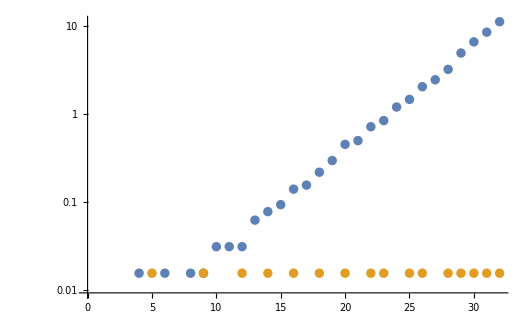

```mathematica
ListLogPlot[{#[[1]]&/@tb,#[[1]]&/@tw}]
```

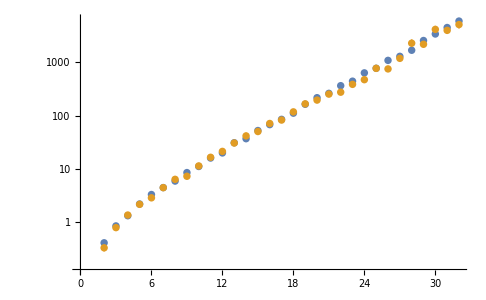

```mathematica
ListLogPlot[{#[[2]]&/@tb,#[[2]]&/@tw}]
```

```mathematica
tw2=Table[{n,PaschenMcPlatesWeighted[n,n,1000]+1},{n,1/2,32,1/2}];
```

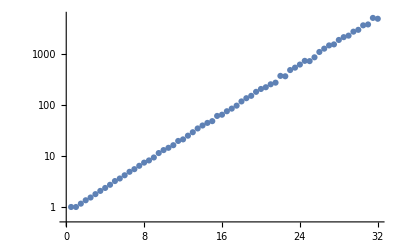

```mathematica
ListLogPlot[tw2]
```

```mathematica
tw2a=Table[{n,PaschenMcPlatesWeighted[n,n,1000]+1},{n,1/10,3,1/10}];
```

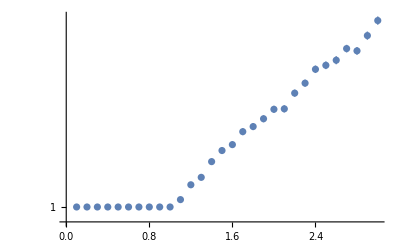

```mathematica
ListLogPlot[tw2a]
```

```mathematica
tw2a$2=Table[{n,PaschenMcPlatesWeighted[n,2n,1000]+1},{n,1/10,3,1/10}];
```

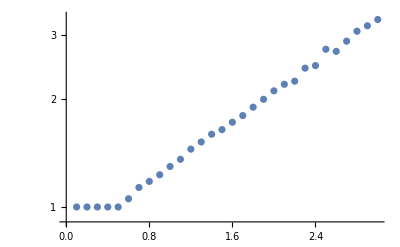

```mathematica
ListLogPlot[tw2a$2]
```

```mathematica
tw$2=Table[{n,PaschenMcPlatesWeighted[n,2n,1000]+1},{n,1/2,20,1/2}];
```

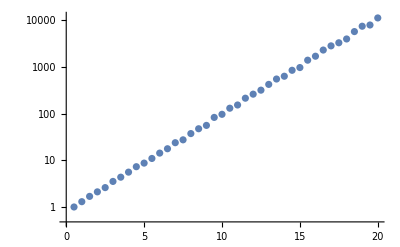

```mathematica
ListLogPlot[tw$2]
```

```mathematica
tw$100=Table[{n,PaschenMcPlatesWeighted[n,n,1000]+1},{n,5,25,5}];
```

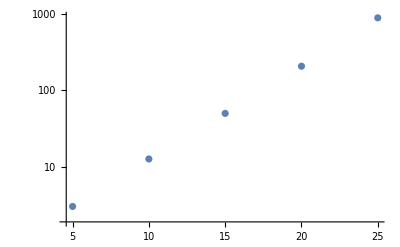

```mathematica
ListLogPlot[tw$100]
```

```mathematica
TableForm[tw$100]
```

5 | 3.050.05
10 | 12.710.35
15 | 49.91.7
20 | 206.8.
25 | 880.37.

```mathematica
slopes=Log[#[[2]]]/(#[[1]]-1)&/@tw$100
```

{0.2790.004,0.28250.0030,0.27930.0025,0.28040.0020,0.28250.0017}

```mathematica
Mean[slopes]
```

0.28080.0012

```mathematica
GetSlope[r_,reps_,range_]:=Module[{tw,slope},
tw=Table[{n,PaschenMcPlatesWeighted[n,r n,reps]+1},{n,range}];
slope=Mean[Log[#[[2]]]/(#[[1]]-1/r)&/@tw];
{r,slope,tw,Show[ListLogPlot[tw],LogPlot[Exp[slope[[1]] (x-1/r)],{x,0,Last[range]},PlotStyle->Red]]}]
```

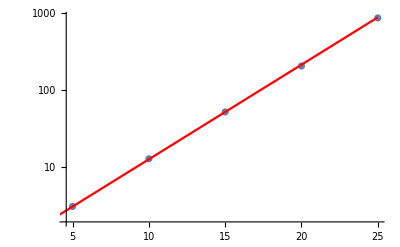
{1,0.28230.0012,{{5,3.110.05},{10,12.860.33},{15,52.11.6},{20,205.8.},{25,862.38.}},-Graphics-}

```mathematica
s$100=GetSlope[1,1000,Range[5,25,5]]
```

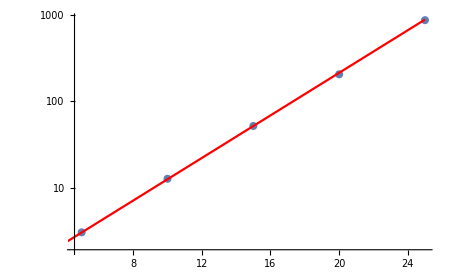

```mathematica
s$100[[4]]
```

```mathematica
SolveFromSlope[s_,invGamma_]:=Module[{},
Log[1+invGamma]/s[[2]]+1/s[[1]]
]
```

```mathematica
sol$100=SolveFromSlope[s$100,50]
```

14.930.06

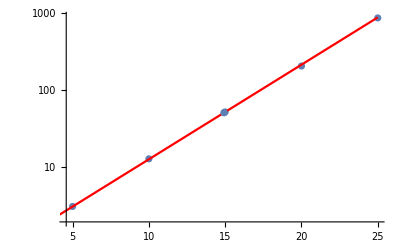

```mathematica
Show[s$100[[4]],ListLogPlot[{{sol$100,51}},PlotStyle->Large]]
```

```mathematica
sol$200=SolveFromSlope[s$200,50]
```

8.7130.034

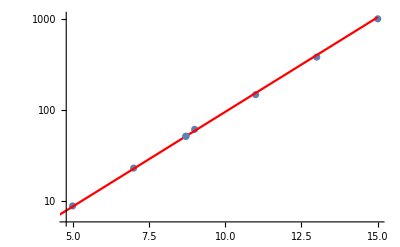

```mathematica
Show[s$200[[4]],ListLogPlot[{{sol$200,51}},PlotStyle->Large]]
```

```mathematica
sols={{sol$19,0.19sol$19},{sol$25,0.25sol$25},{sol$50,0.5sol$50},{sol$75,0.75sol$75},{sol$100,sol$100},{sol$150,1.5sol$150},{sol$200,2 sol$200},{sol$250,2.5 sol$250},{sol$300,3 sol$300},{sol$500,5 sol$500},{sol$1000,10 sol$1000},{sol$2000,20 sol$2000},{sol$4000,40 sol$4000},{sol$8000,80 sol$8000}};
```

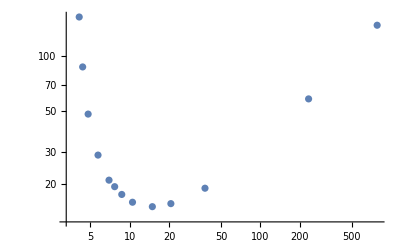

```mathematica
ListLogLogPlot[sols]
```

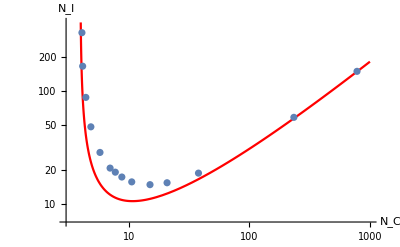

```mathematica
Show[
LogLogPlot[nc/(Log[nc]-Log[Log[51]]),{nc,3.9,1000},
PlotStyle->Red,PlotRange->{{3,1000},{7,400}},
AxesLabel->{"N_C","N_I"}],ListLogLogPlot[sols]
]
```

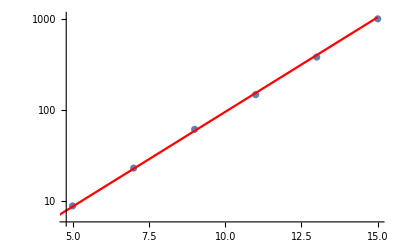
{2,0.47870.0020,{{5,8.780.23},{7,22.80.8},{9,60.82.6},{11,146.6.},{13,378.18.},{15,993.61.}},-Graphics-}

```mathematica
s$200=GetSlope[2,1000,Range[5,15,2]]
```

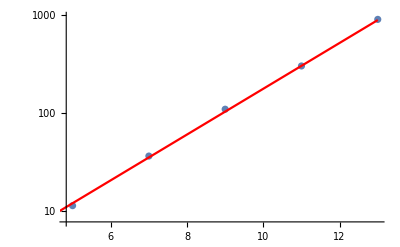
{5/2,0.53930.0027,{{5,11.280.35},{7,36.31.5},{9,109.5.},{11,303.18.},{13,908.65.}},-Graphics-}

```mathematica
s$250=GetSlope[5/2,1000,Range[5,14,2]]
```

```mathematica
sol$250=SolveFromSlope[s$250,50]
```

7.690.04

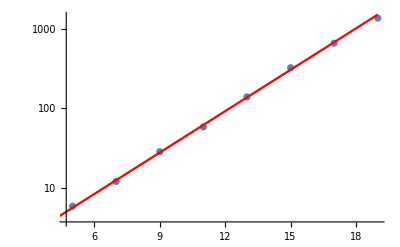
{3/2,0.39880.0013,{{5,5.880.13},{7,12.040.31},{9,28.41.0},{11,58.31.9},{13,139.6.},{15,322.15.},{17,655.33.},{19,1351.67.}},-Graphics-}

```mathematica
s$150=GetSlope[3/2,1000,Range[5,20,2]]
```

```mathematica
sol$150=SolveFromSlope[s$150,50]
```

10.5270.032

```mathematica
sol$300=SolveFromSlope[s$300,50]
```

6.9600.023

```mathematica
sol$500=SolveFromSlope[s$500,50]
```

5.7360.025

```mathematica
sol$1000=SolveFromSlope[s$1000,50]
```

4.8200.024

```mathematica
sol$50=SolveFromSlope[s$50,50]
```

37.710.15

```mathematica
sol$25=SolveFromSlope[s$25,50]
```

233.71.4

```mathematica
sol$75=SolveFromSlope[s$75,50]
```

20.680.05

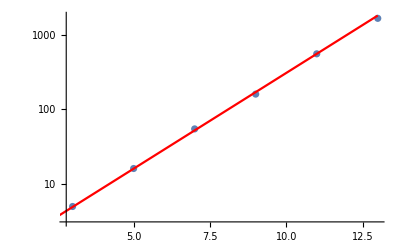
{3,0.59330.0020,{{3,4.940.08},{5,16.00.4},{7,54.72.1},{9,161.5.},{11,560.26.},{13,1683.101.}},-Graphics-}

```mathematica
s$300=GetSlope[3,3000,Range[3,14,2]]
```

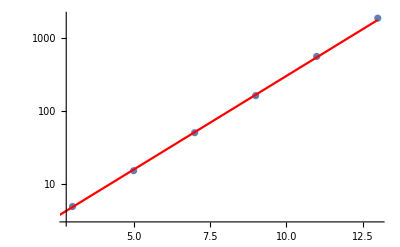
{3,0.59100.0019,{{3,4.910.07},{5,15.220.32},{7,50.61.6},{9,163.5.},{11,564.32.},{13,1887.105.}},-Graphics-}

```mathematica
s$300a=GetSlope[3,3000,Range[3,14,2]]
```

```mathematica
s$150
```

{3/2,0.39880.0013,{{5,5.880.13},{7,12.040.31},{9,28.41.0},{11,58.31.9},{13,139.6.},{15,322.15.},{17,655.33.},{19,1351.67.}},-Graphics-}

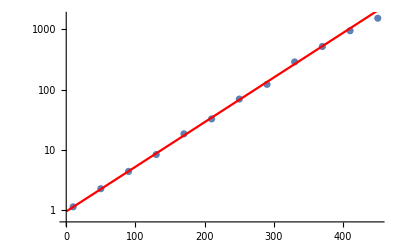
{1/4,0.017120.00010,{{10,1.1140.006},{50,2.2330.033},{90,4.330.09},{130,8.280.23},{170,18.31.0},{210,32.41.5},{250,69.5.},{290,122.9.},{330,288.23.},{370,520.56.},{410,951.72.},{450,1536.109.}},-Graphics-}

```mathematica
s$25
```

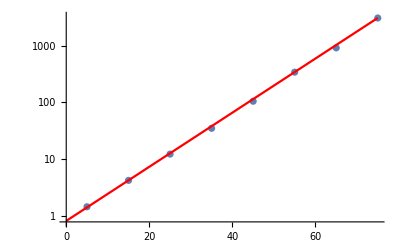
{1/2,0.11010.0005,{{5,1.4270.012},{15,4.170.07},{25,12.150.29},{35,34.71.0},{45,104.43.5},{55,341.18.},{65,915.40.},{75,3082.201.}},-Graphics-}

```mathematica
s$50
```

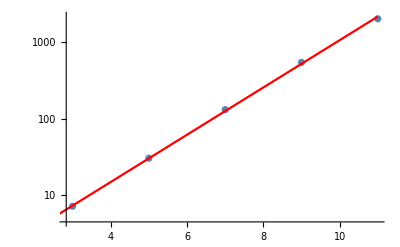
{5,0.71020.0032,{{3,7.170.16},{5,30.41.1},{7,131.5.},{9,540.36.},{11,2009.143.}},-Graphics-}

```mathematica
s$500=GetSlope[5,3000,Range[3,12,2]]
```

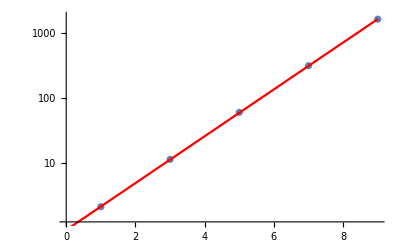
{10,0.8330.004,{{1,2.1030.021},{3,11.290.23},{5,60.12.3},{7,317.19.},{9,1654.166.}},-Graphics-}

```mathematica
s$1000=GetSlope[10,6000,Range[1,9,2]]
```

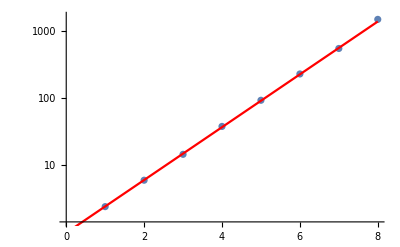
{20,0.9090.004,{{1,2.3550.029},{2,5.840.12},{3,14.20.4},{4,37.21.5},{5,91.5.},{6,226.16.},{7,543.38.},{8,1477.156.}},-Graphics-}

```mathematica
s$2000=GetSlope[20,6000,Range[1,8,1]]
```

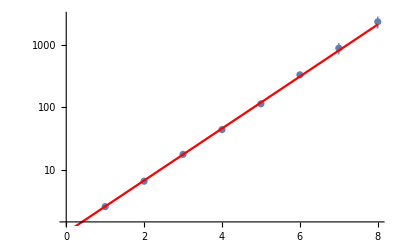
{40,0.9600.007,{{1,2.540.04},{2,6.490.15},{3,17.50.9},{4,43.71.8},{5,113.6.},{6,331.32.},{7,885.184.},{8,2346.513.}},-Graphics-}

```mathematica
s$4000=GetSlope[40,6000,Range[1,8,1]]
```

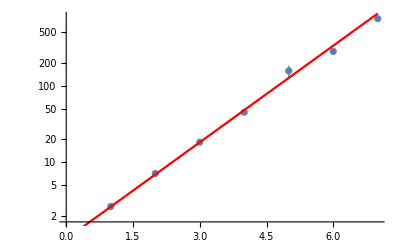
{80,0.9710.007,{{1,2.630.04},{2,7.110.20},{3,18.20.6},{4,45.02.2},{5,157.26.},{6,282.25.},{7,756.52.}},-Graphics-}

```mathematica
s$8000=GetSlope[80,6000,Range[1,7,1]]
```

```mathematica
sol$4000=SolveFromSlope[s$4000,50]
```

4.1190.028

```mathematica
sol$8000=SolveFromSlope[s$8000,50]
```

4.0620.027

```mathematica
sol$2000=SolveFromSlope[s$2000,50]
```

4.3770.019

```mathematica
Log[51.0]
```

3.93183

```mathematica
s$50=GetSlope[1/2,2000,Range[5,80,10]]
```

{1/2,0.11010.0005,{{5,1.4270.012},{15,4.170.07},{25,12.150.29},{35,34.71.0},{45,104.43.5},{55,341.18.},{65,915.40.},{75,3082.201.}},-Graphics-}

```mathematica
Range[5,80,10]
```

{5,15,25,35,45,55,65,75}

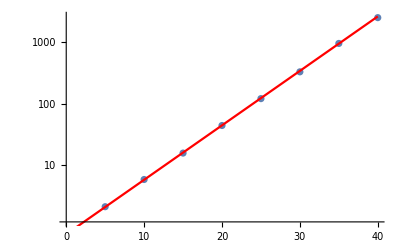
{3/4,0.20320.0006,{{5,2.1320.022},{10,5.890.09},{15,15.770.30},{20,44.11.0},{25,120.33.2},{30,327.10.},{35,943.35.},{40,2471.112.}},-Graphics-}

```mathematica
s$75=GetSlope[3/4,2000,Range[5,40,5]]
```

```mathematica
s$25=GetSlope[1/4,3000,Range[10,460,40]]
```

{1/4,0.017120.00010,{{10,1.1140.006},{50,2.2330.033},{90,4.330.09},{130,8.280.23},{170,18.31.0},{210,32.41.5},{250,69.5.},{290,122.9.},{330,288.23.},{370,520.56.},{410,951.72.},{450,1536.109.}},-Graphics-}

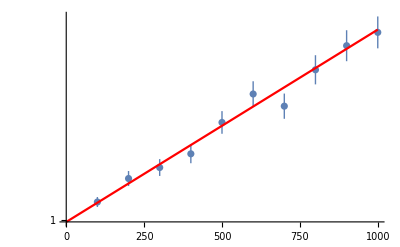
{1/10,0.000046122,{{100,1.00430.0012},{200,1.01000.0018},{300,1.01270.0020},{400,1.01600.0023},{500,1.02370.0028},{600,1.03070.0031},{700,1.02770.0031},{800,1.0370.004},{900,1.0430.004},{1000,1.0460.004}},-Graphics-}

```mathematica
s$10=GetSlope[1/10,3000,Range[100,1000,100]]
```

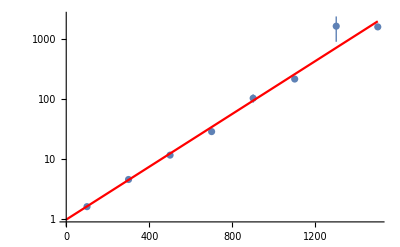
{0.19,0.005070.00006,{{100,1.5990.020},{300,4.530.12},{500,11.50.4},{700,28.41.3},{900,102.16.},{1100,213.14.},{1300,1617.729.},{1500,1572.159.}},-Graphics-}

```mathematica
s$19=GetSlope[0.19,3000,Range[100,1500,200]]
```

```mathematica
sol$19=SolveFromSlope[s$19,50]
```

781.8.

```mathematica
alphas={1/#[[1]],#[[2]]}&/@{s$25,s$50,s$75,s$100,s$150,s$200,s$250,s$300,s$500,s$1000}
```

{{4,0.017300.00011},{2,0.10960.0005},{4/3,0.20450.0006},{1,0.28130.0013},{2/3,0.39970.0013},{1/2,0.47880.0020},{2/5,0.53860.0029},{1/3,0.58970.0019},{1/5,0.71340.0031},{1/10,0.8310.004}}

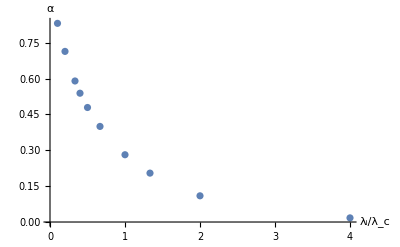

```mathematica
ListPlot[alphas,AxesLabel->{Subscript[λ, i]/Subscript[λ, c],α}]
```

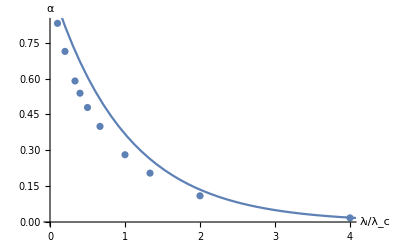

```mathematica
Show[ListPlot[alphas,AxesLabel->{Subscript[λ, i]/Subscript[λ, c],α}],Plot[Exp[-x],{x,0,5}]]
```

```mathematica
alphasInv={#[[1]],#[[2]]}&/@{s$19,s$25,s$50,s$75,s$100,s$150,s$200,s$250,s$300,s$500,s$1000}
```

{{0.19,0.005030.00004},{1/4,0.017300.00011},{1/2,0.10960.0005},{3/4,0.20450.0006},{1,0.28130.0013},{3/2,0.39970.0013},{2,0.47880.0020},{5/2,0.53860.0029},{3,0.58970.0019},{5,0.71340.0031},{10,0.8310.004}}

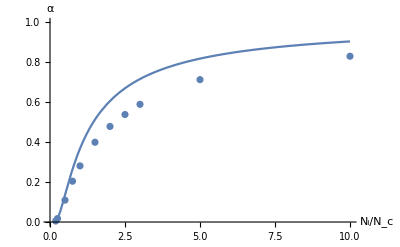

```mathematica
Show[ListPlot[alphasInv,AxesLabel->{Subscript[N, i]/Subscript[N, c],α},PlotRange->{All,{0,1}}],Plot[Exp[-1/x],{x,0.1,10}]]
```

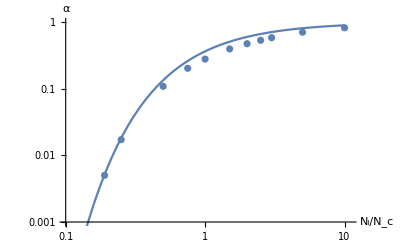

```mathematica
Show[ListPlot[alphasInv,AxesLabel->{Subscript[N, i]/Subscript[N, c],α},ScalingFunctions->{"Log","Log"},PlotRange->{{0.1,11},{0.001,1}}],LogLogPlot[Exp[-1/x],{x,0.1,10}]]
```